### Define Σij=σi@σj

```mathematica
For[i=0,i≤3,i++,For[j=0,j≤3,j++,Σ[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

### Define Hamiltonian with parameters

```mathematica
m=2.5;
t0=1;
t0'=1;
t0''=1;
t=1;
t'=1;
t''=1;
ϕ=Pi/2;
```

```mathematica
Ham[kx_,ky_,kz_]:=(m-t0 Cos[kx]-t0' Cos[ky]-t0'' Cos[kz])Σ[0][3]+t Sin[(kx-ϕ)/2](Sin[kx/2] Σ[1][1]+Cos[kx/2] Σ[2][1])+t' Sin[ky] Σ[0][2]+t'' Sin[kz]Σ[3][1]
```

```mathematica
MatrixForm[Ham[kx,ky,kz]]
```

(2.5-Cos[kx]-Cos[ky]-Cos[kz] | -ⅈ Sin[ky]+Sin[kz] | 0 | (-ⅈ Cos[kx/2]+Sin[kx/2]) Sin[1/2 (kx-π/2)]
ⅈ Sin[ky]+Sin[kz] | -2.5+Cos[kx]+Cos[ky]+Cos[kz] | (-ⅈ Cos[kx/2]+Sin[kx/2]) Sin[1/2 (kx-π/2)] | 0
0 | (ⅈ Cos[kx/2]+Sin[kx/2]) Sin[1/2 (kx-π/2)] | 2.5-Cos[kx]-Cos[ky]-Cos[kz] | -ⅈ Sin[ky]-Sin[kz]
(ⅈ Cos[kx/2]+Sin[kx/2]) Sin[1/2 (kx-π/2)] | 0 | ⅈ Sin[ky]-Sin[kz] | -2.5+Cos[kx]+Cos[ky]+Cos[kz])

### Define dispersion function and plot

```mathematica
F[kx_,ky_,kz_]:=Sort[N[Eigenvalues[Ham[kx+0.0,ky+0.0,kz+0.0]]]];
```

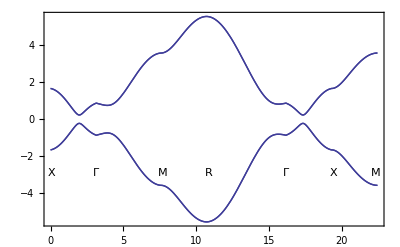

```mathematica
Plot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi},GridLines->{{{Pi,Dashed},{(1+Sqrt[2])Pi,Dashed},{(Sqrt[2]+2)Pi,Dashed},{(2+Sqrt[2]+Sqrt[3])Pi,Dashed},{(3+Sqrt[2]+Sqrt[3])Pi,Dashed},{(4+Sqrt[2]+Sqrt[3])Pi,Dashed}},{}},Epilog->{Inset["X",{0.05,0.08-3}],Inset["Γ",{Pi,0.08-3}],Inset["M",{(1+Sqrt[2])Pi+0.15,0.08-3}],Inset["R",{(2+Sqrt[2])Pi+0.15,0.08-3}],Inset["Γ",{(2+Sqrt[2]+Sqrt[3])Pi,0.08-3}],Inset["X",{(3+Sqrt[2]+Sqrt[3])Pi+0.15,0.08-3}],Inset["M",{(4+Sqrt[2]+Sqrt[3])Pi-0.15,0.08-3}]},Frame->True]
```

### Find the eigensystem and choose the two lower bands as VEC

```mathematica
ESYS[kx_,ky_,kz_]:=Eigensystem[Ham[kx,ky,kz]]
```

```mathematica
VEC[kx_,ky_,kz_]:=(Clear[VEC1,VEC2];For[i=1;j=1,i≤4,i++,If[ESYS[kx,ky,kz][[1]][[i]]<0,If[j==1,VEC1=ESYS[kx,ky,kz][[2]][[i]];j++,VEC2=ESYS[kx,ky,kz][[2]][[i]]]]];{VEC1,VEC2})
```

```mathematica
VEC[1,1,1]
```

{{0.0503578-0.0921792 ⅈ,0.,0.313939+0.313939 ⅈ,0.889861},{0.306826-0.320894 ⅈ,-0.889637+0.0199372 ⅈ,-0.0524104-0.0910279 ⅈ,0.}}

#### define numerical integral function

```mathematica
INT[x_,ky_,kz_,LL_,HL_,i_,j_]:=(Clear[int];
For[ii=LL;int=0,ii≤HL,ii=ii+0.1,int+=0.1x[ii,ky,kz,i,j]]/2/Pi;int)
```

#### define the Core of Correlation function for integral

```mathematica
CORE[kx_,ky_,kz_,i_,j_]:=Exp[I (i-j) kx](KroneckerProduct[Conjugate[VEC[kx,ky,kz][[1]]],VEC[kx,ky,kz][[1]]]+KroneckerProduct[Conjugate[VEC[kx,ky,kz][[2]]],VEC[kx,ky,kz][[2]]])
```

#### define the Correlation function matrix, with 24 by 24

```mathematica
HCOR[ky_,kz_]:=(Clear[COR];Clear[OUT];OUT=Table[COR[i][j],{i,6},{j,6}];For[iii=1,iii≤6,iii++,For[jjj=1,jjj≤6,jjj++,COR[iii][jjj]=INT[CORE ,ky,kz,-Pi,Pi,iii,jjj]]];OUT=ArrayFlatten[OUT])
```

```mathematica
MatrixForm[N[HCOR[1,1]]]
```

(1.09087+0. ⅈ | -1.42119-1.42119 ⅈ | -1.48579×10^-16-5.46221×10^-17 ⅈ | -0.659482+0.189249 ⅈ | 0.381599+0.0274876 ⅈ | -0.305322-0.263736 ⅈ | -7.25844×10^-18-3.434×10^-17 ⅈ | -0.136831+0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | -0.0550612-0.0307054 ⅈ | 5.85765×10^-18-3.70293×10^-17 ⅈ | -0.0239598+0.00930613 ⅈ | 0.0202663-0.000907771 ⅈ | -0.00290373+0.00620764 ⅈ | 5.67168×10^-18+7.24179×10^-17 ⅈ | 0.00192437+0.00223177 ⅈ | 0.00442189-0.000784499 ⅈ | -0.00113973-0.000109518 ⅈ | -3.70959×10^-18-2.30272×10^-17 ⅈ | -0.00208435-0.000342228 ⅈ | -0.00124314-0.000679435 ⅈ | 0.00259236+0.00376286 ⅈ | -1.04294×10^-17+1.54356×10^-18 ⅈ | 0.00315066+0.00061623 ⅈ
-1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | -0.659482+0.189249 ⅈ | -3.64292×10^-18+5.11743×10^-18 ⅈ | -0.263736+0.305322 ⅈ | -0.398406-0.0281871 ⅈ | -0.136831+0.0436676 ⅈ | 1.75395×10^-17+7.81855×10^-18 ⅈ | -0.0307054+0.0550612 ⅈ | -0.0873573-0.00477999 ⅈ | -0.0239598+0.00930613 ⅈ | -1.45929×10^-17-8.24864×10^-18 ⅈ | 0.00620764+0.00290373 ⅈ | -0.0370113-0.00119254 ⅈ | 0.00192437+0.00223177 ⅈ | -6.36274×10^-18+5.63359×10^-18 ⅈ | -0.000109518+0.00113973 ⅈ | 0.0122686+0.00358721 ⅈ | -0.00208435-0.000342228 ⅈ | 2.08177×10^-17-6.69637×10^-18 ⅈ | 0.00376286-0.00259236 ⅈ | -0.015377-0.00282765 ⅈ | 0.00315066+0.00061623 ⅈ | -1.19523×10^-17+2.24257×10^-18 ⅈ
-1.48579×10^-16+5.46221×10^-17 ⅈ | -0.659482-0.189249 ⅈ | 1.09087+0. ⅈ | 1.42119-1.42119 ⅈ | 3.94897×10^-17-1.44327×10^-16 ⅈ | 0.659482-0.189249 ⅈ | 0.381599+0.0274876 ⅈ | 0.263736-0.305322 ⅈ | 3.70155×10^-17-1.31435×10^-17 ⅈ | 0.136831-0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | 0.0307054-0.0550612 ⅈ | 3.56323×10^-17-3.96547×10^-18 ⅈ | 0.0239598-0.00930613 ⅈ | 0.0202663-0.000907771 ⅈ | -0.00620764-0.00290373 ⅈ | -6.83498×10^-17-2.17246×10^-18 ⅈ | -0.00192437-0.00223177 ⅈ | 0.00442189-0.000784499 ⅈ | 0.000109518-0.00113973 ⅈ | 2.43529×10^-17-7.78682×10^-18 ⅈ | 0.00208435+0.000342228 ⅈ | -0.00124314-0.000679435 ⅈ | -0.00376286+0.00259236 ⅈ
-0.659482-0.189249 ⅈ | -3.64292×10^-18-5.11743×10^-18 ⅈ | 1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | 0.659482-0.189249 ⅈ | -6.77998×10^-18+1.93253×10^-17 ⅈ | 0.305322+0.263736 ⅈ | -0.398406-0.0281871 ⅈ | 0.136831-0.0436676 ⅈ | 6.31342×10^-18-1.40563×10^-17 ⅈ | 0.0550612+0.0307054 ⅈ | -0.0873573-0.00477999 ⅈ | 0.0239598-0.00930613 ⅈ | -5.67063×10^-18-8.27684×10^-18 ⅈ | 0.00290373-0.00620764 ⅈ | -0.0370113-0.00119254 ⅈ | -0.00192437-0.00223177 ⅈ | 8.44006×10^-18+2.12135×10^-17 ⅈ | 0.00113973+0.000109518 ⅈ | 0.0122686+0.00358721 ⅈ | 0.00208435+0.000342228 ⅈ | -2.95676×10^-18-1.04825×10^-17 ⅈ | -0.00259236-0.00376286 ⅈ | -0.015377-0.00282765 ⅈ
0.381599-0.0274876 ⅈ | -0.263736-0.305322 ⅈ | 3.94897×10^-17+1.44327×10^-16 ⅈ | 0.659482+0.189249 ⅈ | 1.09087+0. ⅈ | -1.42119-1.42119 ⅈ | -1.48579×10^-16-5.46221×10^-17 ⅈ | -0.659482+0.189249 ⅈ | 0.381599+0.0274876 ⅈ | -0.305322-0.263736 ⅈ | -7.25844×10^-18-3.434×10^-17 ⅈ | -0.136831+0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | -0.0550612-0.0307054 ⅈ | 5.85765×10^-18-3.70293×10^-17 ⅈ | -0.0239598+0.00930613 ⅈ | 0.0202663-0.000907771 ⅈ | -0.00290373+0.00620764 ⅈ | 5.67168×10^-18+7.24179×10^-17 ⅈ | 0.00192437+0.00223177 ⅈ | 0.00442189-0.000784499 ⅈ | -0.00113973-0.000109518 ⅈ | -3.70959×10^-18-2.30272×10^-17 ⅈ | -0.00208435-0.000342228 ⅈ
-0.305322+0.263736 ⅈ | -0.398406+0.0281871 ⅈ | 0.659482+0.189249 ⅈ | -6.77998×10^-18-1.93253×10^-17 ⅈ | -1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | -0.659482+0.189249 ⅈ | -3.64292×10^-18+5.11743×10^-18 ⅈ | -0.263736+0.305322 ⅈ | -0.398406-0.0281871 ⅈ | -0.136831+0.0436676 ⅈ | 1.75395×10^-17+7.81855×10^-18 ⅈ | -0.0307054+0.0550612 ⅈ | -0.0873573-0.00477999 ⅈ | -0.0239598+0.00930613 ⅈ | -1.45929×10^-17-8.24864×10^-18 ⅈ | 0.00620764+0.00290373 ⅈ | -0.0370113-0.00119254 ⅈ | 0.00192437+0.00223177 ⅈ | -6.36274×10^-18+5.63359×10^-18 ⅈ | -0.000109518+0.00113973 ⅈ | 0.0122686+0.00358721 ⅈ | -0.00208435-0.000342228 ⅈ | 2.08177×10^-17-6.69637×10^-18 ⅈ
-7.25844×10^-18+3.434×10^-17 ⅈ | -0.136831-0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | 0.305322-0.263736 ⅈ | -1.48579×10^-16+5.46221×10^-17 ⅈ | -0.659482-0.189249 ⅈ | 1.09087+0. ⅈ | 1.42119-1.42119 ⅈ | 3.94897×10^-17-1.44327×10^-16 ⅈ | 0.659482-0.189249 ⅈ | 0.381599+0.0274876 ⅈ | 0.263736-0.305322 ⅈ | 3.70155×10^-17-1.31435×10^-17 ⅈ | 0.136831-0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | 0.0307054-0.0550612 ⅈ | 3.56323×10^-17-3.96547×10^-18 ⅈ | 0.0239598-0.00930613 ⅈ | 0.0202663-0.000907771 ⅈ | -0.00620764-0.00290373 ⅈ | -6.83498×10^-17-2.17246×10^-18 ⅈ | -0.00192437-0.00223177 ⅈ | 0.00442189-0.000784499 ⅈ | 0.000109518-0.00113973 ⅈ
-0.136831-0.0436676 ⅈ | 1.75395×10^-17-7.81855×10^-18 ⅈ | 0.263736+0.305322 ⅈ | -0.398406+0.0281871 ⅈ | -0.659482-0.189249 ⅈ | -3.64292×10^-18-5.11743×10^-18 ⅈ | 1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | 0.659482-0.189249 ⅈ | -6.77998×10^-18+1.93253×10^-17 ⅈ | 0.305322+0.263736 ⅈ | -0.398406-0.0281871 ⅈ | 0.136831-0.0436676 ⅈ | 6.31342×10^-18-1.40563×10^-17 ⅈ | 0.0550612+0.0307054 ⅈ | -0.0873573-0.00477999 ⅈ | 0.0239598-0.00930613 ⅈ | -5.67063×10^-18-8.27684×10^-18 ⅈ | 0.00290373-0.00620764 ⅈ | -0.0370113-0.00119254 ⅈ | -0.00192437-0.00223177 ⅈ | 8.44006×10^-18+2.12135×10^-17 ⅈ | 0.00113973+0.000109518 ⅈ | 0.0122686+0.00358721 ⅈ
0.104141-0.00617938 ⅈ | -0.0307054-0.0550612 ⅈ | 3.70155×10^-17+1.31435×10^-17 ⅈ | 0.136831+0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | -0.263736-0.305322 ⅈ | 3.94897×10^-17+1.44327×10^-16 ⅈ | 0.659482+0.189249 ⅈ | 1.09087+0. ⅈ | -1.42119-1.42119 ⅈ | -1.48579×10^-16-5.46221×10^-17 ⅈ | -0.659482+0.189249 ⅈ | 0.381599+0.0274876 ⅈ | -0.305322-0.263736 ⅈ | -7.25844×10^-18-3.434×10^-17 ⅈ | -0.136831+0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | -0.0550612-0.0307054 ⅈ | 5.85765×10^-18-3.70293×10^-17 ⅈ | -0.0239598+0.00930613 ⅈ | 0.0202663-0.000907771 ⅈ | -0.00290373+0.00620764 ⅈ | 5.67168×10^-18+7.24179×10^-17 ⅈ | 0.00192437+0.00223177 ⅈ
-0.0550612+0.0307054 ⅈ | -0.0873573+0.00477999 ⅈ | 0.136831+0.0436676 ⅈ | 6.31342×10^-18+1.40563×10^-17 ⅈ | -0.305322+0.263736 ⅈ | -0.398406+0.0281871 ⅈ | 0.659482+0.189249 ⅈ | -6.77998×10^-18-1.93253×10^-17 ⅈ | -1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | -0.659482+0.189249 ⅈ | -3.64292×10^-18+5.11743×10^-18 ⅈ | -0.263736+0.305322 ⅈ | -0.398406-0.0281871 ⅈ | -0.136831+0.0436676 ⅈ | 1.75395×10^-17+7.81855×10^-18 ⅈ | -0.0307054+0.0550612 ⅈ | -0.0873573-0.00477999 ⅈ | -0.0239598+0.00930613 ⅈ | -1.45929×10^-17-8.24864×10^-18 ⅈ | 0.00620764+0.00290373 ⅈ | -0.0370113-0.00119254 ⅈ | 0.00192437+0.00223177 ⅈ | -6.36274×10^-18+5.63359×10^-18 ⅈ
5.85765×10^-18+3.70293×10^-17 ⅈ | -0.0239598-0.00930613 ⅈ | 0.104141-0.00617938 ⅈ | 0.0550612-0.0307054 ⅈ | -7.25844×10^-18+3.434×10^-17 ⅈ | -0.136831-0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | 0.305322-0.263736 ⅈ | -1.48579×10^-16+5.46221×10^-17 ⅈ | -0.659482-0.189249 ⅈ | 1.09087+0. ⅈ | 1.42119-1.42119 ⅈ | 3.94897×10^-17-1.44327×10^-16 ⅈ | 0.659482-0.189249 ⅈ | 0.381599+0.0274876 ⅈ | 0.263736-0.305322 ⅈ | 3.70155×10^-17-1.31435×10^-17 ⅈ | 0.136831-0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | 0.0307054-0.0550612 ⅈ | 3.56323×10^-17-3.96547×10^-18 ⅈ | 0.0239598-0.00930613 ⅈ | 0.0202663-0.000907771 ⅈ | -0.00620764-0.00290373 ⅈ
-0.0239598-0.00930613 ⅈ | -1.45929×10^-17+8.24864×10^-18 ⅈ | 0.0307054+0.0550612 ⅈ | -0.0873573+0.00477999 ⅈ | -0.136831-0.0436676 ⅈ | 1.75395×10^-17-7.81855×10^-18 ⅈ | 0.263736+0.305322 ⅈ | -0.398406+0.0281871 ⅈ | -0.659482-0.189249 ⅈ | -3.64292×10^-18-5.11743×10^-18 ⅈ | 1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | 0.659482-0.189249 ⅈ | -6.77998×10^-18+1.93253×10^-17 ⅈ | 0.305322+0.263736 ⅈ | -0.398406-0.0281871 ⅈ | 0.136831-0.0436676 ⅈ | 6.31342×10^-18-1.40563×10^-17 ⅈ | 0.0550612+0.0307054 ⅈ | -0.0873573-0.00477999 ⅈ | 0.0239598-0.00930613 ⅈ | -5.67063×10^-18-8.27684×10^-18 ⅈ | 0.00290373-0.00620764 ⅈ | -0.0370113-0.00119254 ⅈ
0.0202663+0.000907771 ⅈ | 0.00620764-0.00290373 ⅈ | 3.56323×10^-17+3.96547×10^-18 ⅈ | 0.0239598+0.00930613 ⅈ | 0.104141-0.00617938 ⅈ | -0.0307054-0.0550612 ⅈ | 3.70155×10^-17+1.31435×10^-17 ⅈ | 0.136831+0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | -0.263736-0.305322 ⅈ | 3.94897×10^-17+1.44327×10^-16 ⅈ | 0.659482+0.189249 ⅈ | 1.09087+0. ⅈ | -1.42119-1.42119 ⅈ | -1.48579×10^-16-5.46221×10^-17 ⅈ | -0.659482+0.189249 ⅈ | 0.381599+0.0274876 ⅈ | -0.305322-0.263736 ⅈ | -7.25844×10^-18-3.434×10^-17 ⅈ | -0.136831+0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | -0.0550612-0.0307054 ⅈ | 5.85765×10^-18-3.70293×10^-17 ⅈ | -0.0239598+0.00930613 ⅈ
-0.00290373-0.00620764 ⅈ | -0.0370113+0.00119254 ⅈ | 0.0239598+0.00930613 ⅈ | -5.67063×10^-18+8.27684×10^-18 ⅈ | -0.0550612+0.0307054 ⅈ | -0.0873573+0.00477999 ⅈ | 0.136831+0.0436676 ⅈ | 6.31342×10^-18+1.40563×10^-17 ⅈ | -0.305322+0.263736 ⅈ | -0.398406+0.0281871 ⅈ | 0.659482+0.189249 ⅈ | -6.77998×10^-18-1.93253×10^-17 ⅈ | -1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | -0.659482+0.189249 ⅈ | -3.64292×10^-18+5.11743×10^-18 ⅈ | -0.263736+0.305322 ⅈ | -0.398406-0.0281871 ⅈ | -0.136831+0.0436676 ⅈ | 1.75395×10^-17+7.81855×10^-18 ⅈ | -0.0307054+0.0550612 ⅈ | -0.0873573-0.00477999 ⅈ | -0.0239598+0.00930613 ⅈ | -1.45929×10^-17-8.24864×10^-18 ⅈ
5.67168×10^-18-7.24179×10^-17 ⅈ | 0.00192437-0.00223177 ⅈ | 0.0202663+0.000907771 ⅈ | 0.00290373+0.00620764 ⅈ | 5.85765×10^-18+3.70293×10^-17 ⅈ | -0.0239598-0.00930613 ⅈ | 0.104141-0.00617938 ⅈ | 0.0550612-0.0307054 ⅈ | -7.25844×10^-18+3.434×10^-17 ⅈ | -0.136831-0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | 0.305322-0.263736 ⅈ | -1.48579×10^-16+5.46221×10^-17 ⅈ | -0.659482-0.189249 ⅈ | 1.09087+0. ⅈ | 1.42119-1.42119 ⅈ | 3.94897×10^-17-1.44327×10^-16 ⅈ | 0.659482-0.189249 ⅈ | 0.381599+0.0274876 ⅈ | 0.263736-0.305322 ⅈ | 3.70155×10^-17-1.31435×10^-17 ⅈ | 0.136831-0.0436676 ⅈ | 0.104141+0.00617938 ⅈ | 0.0307054-0.0550612 ⅈ
0.00192437-0.00223177 ⅈ | -6.36274×10^-18-5.63359×10^-18 ⅈ | -0.00620764+0.00290373 ⅈ | -0.0370113+0.00119254 ⅈ | -0.0239598-0.00930613 ⅈ | -1.45929×10^-17+8.24864×10^-18 ⅈ | 0.0307054+0.0550612 ⅈ | -0.0873573+0.00477999 ⅈ | -0.136831-0.0436676 ⅈ | 1.75395×10^-17-7.81855×10^-18 ⅈ | 0.263736+0.305322 ⅈ | -0.398406+0.0281871 ⅈ | -0.659482-0.189249 ⅈ | -3.64292×10^-18-5.11743×10^-18 ⅈ | 1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | 0.659482-0.189249 ⅈ | -6.77998×10^-18+1.93253×10^-17 ⅈ | 0.305322+0.263736 ⅈ | -0.398406-0.0281871 ⅈ | 0.136831-0.0436676 ⅈ | 6.31342×10^-18-1.40563×10^-17 ⅈ | 0.0550612+0.0307054 ⅈ | -0.0873573-0.00477999 ⅈ
0.00442189+0.000784499 ⅈ | -0.000109518-0.00113973 ⅈ | -6.83498×10^-17+2.17246×10^-18 ⅈ | -0.00192437+0.00223177 ⅈ | 0.0202663+0.000907771 ⅈ | 0.00620764-0.00290373 ⅈ | 3.56323×10^-17+3.96547×10^-18 ⅈ | 0.0239598+0.00930613 ⅈ | 0.104141-0.00617938 ⅈ | -0.0307054-0.0550612 ⅈ | 3.70155×10^-17+1.31435×10^-17 ⅈ | 0.136831+0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | -0.263736-0.305322 ⅈ | 3.94897×10^-17+1.44327×10^-16 ⅈ | 0.659482+0.189249 ⅈ | 1.09087+0. ⅈ | -1.42119-1.42119 ⅈ | -1.48579×10^-16-5.46221×10^-17 ⅈ | -0.659482+0.189249 ⅈ | 0.381599+0.0274876 ⅈ | -0.305322-0.263736 ⅈ | -7.25844×10^-18-3.434×10^-17 ⅈ | -0.136831+0.0436676 ⅈ
-0.00113973+0.000109518 ⅈ | 0.0122686-0.00358721 ⅈ | -0.00192437+0.00223177 ⅈ | 8.44006×10^-18-2.12135×10^-17 ⅈ | -0.00290373-0.00620764 ⅈ | -0.0370113+0.00119254 ⅈ | 0.0239598+0.00930613 ⅈ | -5.67063×10^-18+8.27684×10^-18 ⅈ | -0.0550612+0.0307054 ⅈ | -0.0873573+0.00477999 ⅈ | 0.136831+0.0436676 ⅈ | 6.31342×10^-18+1.40563×10^-17 ⅈ | -0.305322+0.263736 ⅈ | -0.398406+0.0281871 ⅈ | 0.659482+0.189249 ⅈ | -6.77998×10^-18-1.93253×10^-17 ⅈ | -1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | -0.659482+0.189249 ⅈ | -3.64292×10^-18+5.11743×10^-18 ⅈ | -0.263736+0.305322 ⅈ | -0.398406-0.0281871 ⅈ | -0.136831+0.0436676 ⅈ | 1.75395×10^-17+7.81855×10^-18 ⅈ
-3.70959×10^-18+2.30272×10^-17 ⅈ | -0.00208435+0.000342228 ⅈ | 0.00442189+0.000784499 ⅈ | 0.00113973-0.000109518 ⅈ | 5.67168×10^-18-7.24179×10^-17 ⅈ | 0.00192437-0.00223177 ⅈ | 0.0202663+0.000907771 ⅈ | 0.00290373+0.00620764 ⅈ | 5.85765×10^-18+3.70293×10^-17 ⅈ | -0.0239598-0.00930613 ⅈ | 0.104141-0.00617938 ⅈ | 0.0550612-0.0307054 ⅈ | -7.25844×10^-18+3.434×10^-17 ⅈ | -0.136831-0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | 0.305322-0.263736 ⅈ | -1.48579×10^-16+5.46221×10^-17 ⅈ | -0.659482-0.189249 ⅈ | 1.09087+0. ⅈ | 1.42119-1.42119 ⅈ | 3.94897×10^-17-1.44327×10^-16 ⅈ | 0.659482-0.189249 ⅈ | 0.381599+0.0274876 ⅈ | 0.263736-0.305322 ⅈ
-0.00208435+0.000342228 ⅈ | 2.08177×10^-17+6.69637×10^-18 ⅈ | 0.000109518+0.00113973 ⅈ | 0.0122686-0.00358721 ⅈ | 0.00192437-0.00223177 ⅈ | -6.36274×10^-18-5.63359×10^-18 ⅈ | -0.00620764+0.00290373 ⅈ | -0.0370113+0.00119254 ⅈ | -0.0239598-0.00930613 ⅈ | -1.45929×10^-17+8.24864×10^-18 ⅈ | 0.0307054+0.0550612 ⅈ | -0.0873573+0.00477999 ⅈ | -0.136831-0.0436676 ⅈ | 1.75395×10^-17-7.81855×10^-18 ⅈ | 0.263736+0.305322 ⅈ | -0.398406+0.0281871 ⅈ | -0.659482-0.189249 ⅈ | -3.64292×10^-18-5.11743×10^-18 ⅈ | 1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | 0.659482-0.189249 ⅈ | -6.77998×10^-18+1.93253×10^-17 ⅈ | 0.305322+0.263736 ⅈ | -0.398406-0.0281871 ⅈ
-0.00124314+0.000679435 ⅈ | 0.00376286+0.00259236 ⅈ | 2.43529×10^-17+7.78682×10^-18 ⅈ | 0.00208435-0.000342228 ⅈ | 0.00442189+0.000784499 ⅈ | -0.000109518-0.00113973 ⅈ | -6.83498×10^-17+2.17246×10^-18 ⅈ | -0.00192437+0.00223177 ⅈ | 0.0202663+0.000907771 ⅈ | 0.00620764-0.00290373 ⅈ | 3.56323×10^-17+3.96547×10^-18 ⅈ | 0.0239598+0.00930613 ⅈ | 0.104141-0.00617938 ⅈ | -0.0307054-0.0550612 ⅈ | 3.70155×10^-17+1.31435×10^-17 ⅈ | 0.136831+0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | -0.263736-0.305322 ⅈ | 3.94897×10^-17+1.44327×10^-16 ⅈ | 0.659482+0.189249 ⅈ | 1.09087+0. ⅈ | -1.42119-1.42119 ⅈ | -1.48579×10^-16-5.46221×10^-17 ⅈ | -0.659482+0.189249 ⅈ
0.00259236-0.00376286 ⅈ | -0.015377+0.00282765 ⅈ | 0.00208435-0.000342228 ⅈ | -2.95676×10^-18+1.04825×10^-17 ⅈ | -0.00113973+0.000109518 ⅈ | 0.0122686-0.00358721 ⅈ | -0.00192437+0.00223177 ⅈ | 8.44006×10^-18-2.12135×10^-17 ⅈ | -0.00290373-0.00620764 ⅈ | -0.0370113+0.00119254 ⅈ | 0.0239598+0.00930613 ⅈ | -5.67063×10^-18+8.27684×10^-18 ⅈ | -0.0550612+0.0307054 ⅈ | -0.0873573+0.00477999 ⅈ | 0.136831+0.0436676 ⅈ | 6.31342×10^-18+1.40563×10^-17 ⅈ | -0.305322+0.263736 ⅈ | -0.398406+0.0281871 ⅈ | 0.659482+0.189249 ⅈ | -6.77998×10^-18-1.93253×10^-17 ⅈ | -1.42119+1.42119 ⅈ | 5.20913+0. ⅈ | -0.659482+0.189249 ⅈ | -3.64292×10^-18+5.11743×10^-18 ⅈ
-1.04294×10^-17-1.54356×10^-18 ⅈ | 0.00315066-0.00061623 ⅈ | -0.00124314+0.000679435 ⅈ | -0.00259236+0.00376286 ⅈ | -3.70959×10^-18+2.30272×10^-17 ⅈ | -0.00208435+0.000342228 ⅈ | 0.00442189+0.000784499 ⅈ | 0.00113973-0.000109518 ⅈ | 5.67168×10^-18-7.24179×10^-17 ⅈ | 0.00192437-0.00223177 ⅈ | 0.0202663+0.000907771 ⅈ | 0.00290373+0.00620764 ⅈ | 5.85765×10^-18+3.70293×10^-17 ⅈ | -0.0239598-0.00930613 ⅈ | 0.104141-0.00617938 ⅈ | 0.0550612-0.0307054 ⅈ | -7.25844×10^-18+3.434×10^-17 ⅈ | -0.136831-0.0436676 ⅈ | 0.381599-0.0274876 ⅈ | 0.305322-0.263736 ⅈ | -1.48579×10^-16+5.46221×10^-17 ⅈ | -0.659482-0.189249 ⅈ | 1.09087+0. ⅈ | 1.42119-1.42119 ⅈ
0.00315066-0.00061623 ⅈ | -1.19523×10^-17-2.24257×10^-18 ⅈ | -0.00376286-0.00259236 ⅈ | -0.015377+0.00282765 ⅈ | -0.00208435+0.000342228 ⅈ | 2.08177×10^-17+6.69637×10^-18 ⅈ | 0.000109518+0.00113973 ⅈ | 0.0122686-0.00358721 ⅈ | 0.00192437-0.00223177 ⅈ | -6.36274×10^-18-5.63359×10^-18 ⅈ | -0.00620764+0.00290373 ⅈ | -0.0370113+0.00119254 ⅈ | -0.0239598-0.00930613 ⅈ | -1.45929×10^-17+8.24864×10^-18 ⅈ | 0.0307054+0.0550612 ⅈ | -0.0873573+0.00477999 ⅈ | -0.136831-0.0436676 ⅈ | 1.75395×10^-17-7.81855×10^-18 ⅈ | 0.263736+0.305322 ⅈ | -0.398406+0.0281871 ⅈ | -0.659482-0.189249 ⅈ | -3.64292×10^-18-5.11743×10^-18 ⅈ | 1.42119+1.42119 ⅈ | 5.20913+0. ⅈ)

#### eigenvalues of Correlation matrix is Pi, we need plot 1/2-Pi

```mathematica
FCOR[kx_,ky_]:=Sort[Eigenvalues[HCOR[kx,ky]]]
```

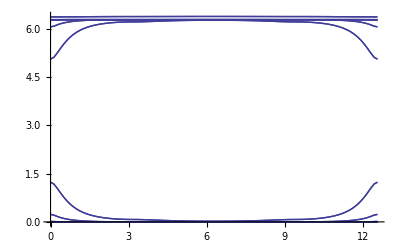

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<3Pi},{FCOR[0,4Pi-T],T≥3Pi&&T≤4Pi}}],{T,0,4Pi,4Pi/100},Filling->None,Evaluate[Joined->True]]
```

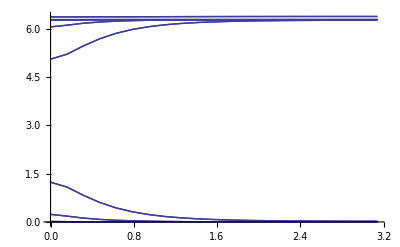

```mathematica
DiscretePlot[FCOR[T,T],{T,0,Pi,Pi/20},Filling->None,Evaluate[Joined->True]]
```

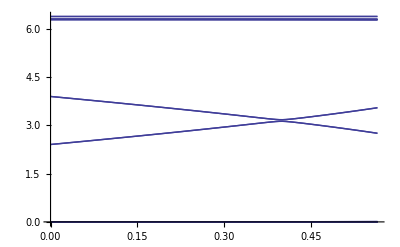

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<3Pi},{FCOR[0,4Pi-T],T≥3Pi&&T≤4Pi}}],{T,0,0.18Pi,0.18Pi/100},Filling->None,Evaluate[Joined->True]]
```

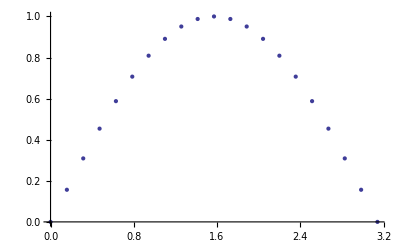

```mathematica
DiscretePlot[Sin[x],{x,0,Pi,Pi/20},Filling->None]
```

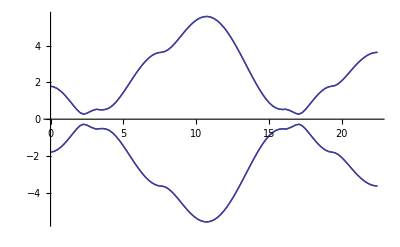

```mathematica
DiscretePlot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi,(4+Sqrt[2]+Sqrt[3])Pi/100},Filling->None,Evaluate[Joined->True]]
```